```mathematica
PARS={r[0]->0.2,γ[0]->50,s[0]->0.9,σ->1,m->0.05,β->1,ϵ->0.05};
```

```mathematica
tMax=500;
```

```mathematica
Δt=10;
```

## Ecological Model

Deterministic Dynamics

```mathematica
Clear[nEco]
nEco[pars_,tmax_,n0_]:=Block[{out,t},out={{0,n0}};
For[t=1,t≤tmax,t++,
AppendTo[out,{t,n(1+r[0] (1-n/γ[0]))s[0]+m/.pars/.n->out[[t,2]]}]
];
out
]
```

Stochastic Dynamics from MatLab

```mathematica
ecoN=Import["/Users/ailenemacpherson/Dropbox/r:K selection files/MatLab/ecoN.csv"]//Chop;
```

```mathematica
{nMax,tMax}=Dimensions[ecoN]-1
```

{45,200}

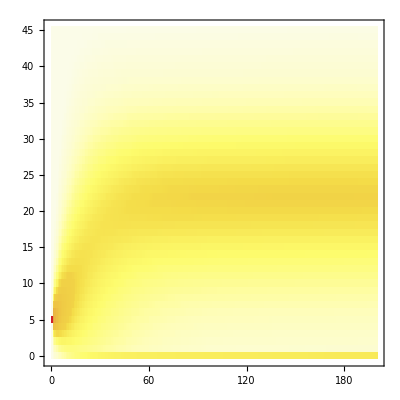

```mathematica
mtrxPlot1=MatrixPlot[ecoN,AspectRatio->1,ColorFunction->"TemperatureMap",FrameTicks->{Table[{i,nMax+1-i},{i,1,nMax+1,5}],Table[{t,t-1},{t,1,tMax+1,20}],False,False}]
```

Combined plots

```mathematica
avgList=Table[ecoN[[;;,t]].Reverse[Table[i,{i,0,nMax}]],{t,1,tMax+1}];
```

```mathematica
avgPlot1=ListLinePlot[avgList,PlotStyle->Red,PlotRange->All];
```

```mathematica
detPlot1=ListLinePlot[nEco[PARS,tMax,5][[1;;tMax,2]],PlotStyle->Blue,PlotRange->All];
```

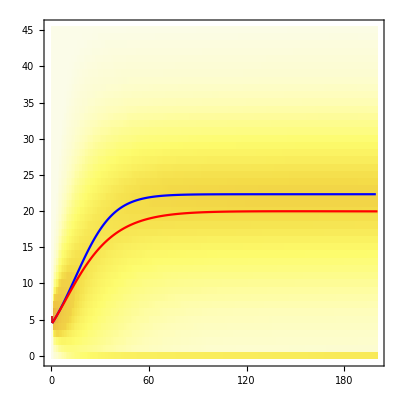

```mathematica
ecoModel=Show[mtrxPlot1,detPlot1,avgPlot1]
```

```mathematica
Export["/Users/ailenemacpherson/Documents/OutPut/ecoModel.gif",ecoModel,ImageResolution->700]
```

/Users/ailenemacpherson/Documents/OutPut/ecoModel.gif

## Evolutionary Model

Deterministic Dynamics

## Density Independent

```mathematica
DIDyn[pars_,n0_,tmax_]:=Block[{out,t,np,s},out={Join[{0},n0]};
np[i_]:=n[i](1+r[0](1-(n[1]+n[2])/γ[0]))s[i]+m/2;
For[t=1,t≤tmax,t++,
AppendTo[out,{t,np[1],np[2]}/.{s[1]->s[0],s[2]->s[0]-σ ϵ}/.pars/.{n[1]->out[[t,2]],n[2]->out[[t,3]]}]
];
out
]
```

```mathematica
diDyn=DIDyn[PARS,{2,2},tMax][[Table[i,{i,1,tMax,Δt}]]];
```

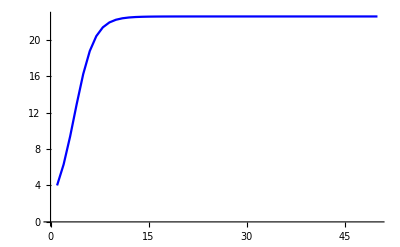

```mathematica
detPlot2=ListLinePlot[diDyn[[;;,2]]+diDyn[[;;,3]],PlotStyle->Blue,PlotRange->All]
```

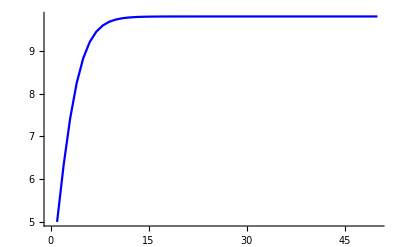

```mathematica
detPlot4=ListLinePlot[diDyn[[;;,2]]/(diDyn[[;;,2]]+diDyn[[;;,3]])nBins,PlotStyle->Blue,PlotRange->All]
```

## Density-dependent

```mathematica
tOffSub[i_]:={γ[i]->γ[0](r[0]/r[i])^β};
```

```mathematica
DDDyn[pars_,n0_,tmax_]:=Block[{out,t,np},out={Join[{0},n0]};
np[i_]:=n[i](1+r[i](1-(n[1]+n[2])/γ[i]))s[0]+m/2/.tOffSub[i];
For[t=1,t≤tmax,t++,
AppendTo[out,{t,np[1],np[2]}/.{r[1]->r[0],r[2]->r[0]+ϵ σ}/.pars/.{n[1]->out[[t,2]],n[2]->out[[t,3]]}]
];
out
]
```

```mathematica
ddDyn=DDDyn[PARS,{2,2},tMax][[Table[i,{i,1,tMax,Δt}]]];
```

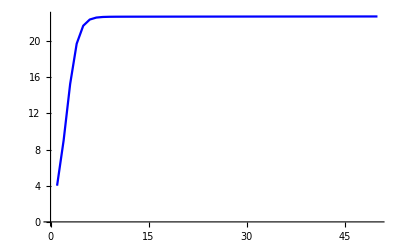

```mathematica
detPlot3=ListLinePlot[ddDyn[[;;,2]]+ddDyn[[;;,3]],PlotStyle->Blue,PlotRange->All]
```

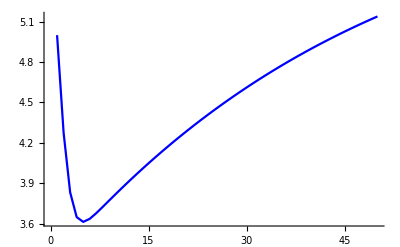

```mathematica
detPlot5=ListLinePlot[ddDyn[[;;,2]]/(ddDyn[[;;,2]]+ddDyn[[;;,3]])nBins,PlotStyle->Blue,PlotRange->All]
```

Stochastic Dynamics

## Population size

### Density Independence

```mathematica
Nmtrx=Import["/Users/ailenemacpherson/Dropbox/r:K selection files/MatLab/DIN.csv"]//Chop;
```

```mathematica
{nMax,nSteps}=Dimensions[Nmtrx]-1
```

{34,50}

```mathematica
Nmtrx2=Transpose[Table[Reverse[Nmtrx[[;;,c]]],{c,1,nSteps+1}]];
```

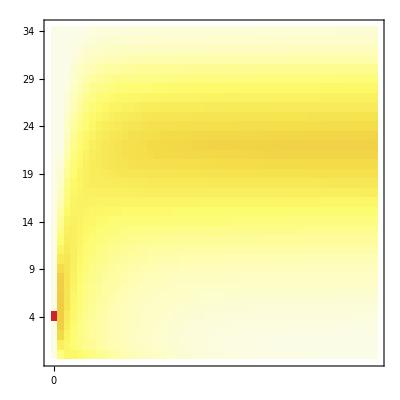

```mathematica
mtrxPlot2=MatrixPlot[Nmtrx2,AspectRatio->1,ColorFunction->"TemperatureMap",FrameTicks->{Table[{i,nMax+1-i},{i,1,nMax+1,5}],Table[{t,(t-1)*Δt},{t,1,tMax+1,10}],False,False}]
```

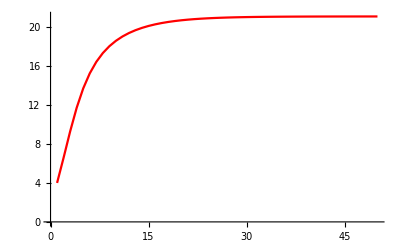

```mathematica
avgPlot2=ListLinePlot[Table[Nmtrx2[[;;,t]].Reverse[Table[i,{i,0,nMax}]],{t,1,nSteps}],PlotStyle->Red,PlotRange->All]
```

### Density Dependence

```mathematica
Nmtrx=Import["/Users/ailenemacpherson/Dropbox/r:K selection files/MatLab/DDN.csv"]//Chop;
```

```mathematica
{nMax,nSteps}=Dimensions[Nmtrx]-1
```

{34,50}

```mathematica
Nmtrx2=Transpose[Table[Reverse[Nmtrx[[;;,c]]],{c,1,nSteps+1}]];
```

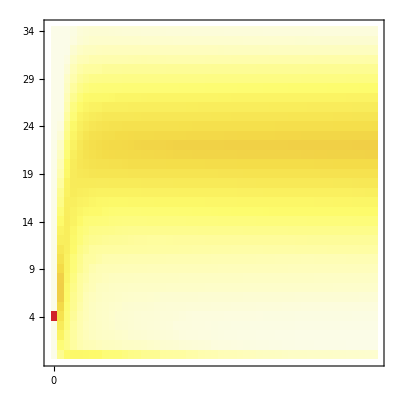

```mathematica
mtrxPlot3=MatrixPlot[Nmtrx2,AspectRatio->1,ColorFunction->"TemperatureMap",FrameTicks->{Table[{i,nMax+1-i},{i,1,nMax+1,5}],Table[{t,(t-1)*Δt},{t,1,tMax+1,10}],False,False}]
```

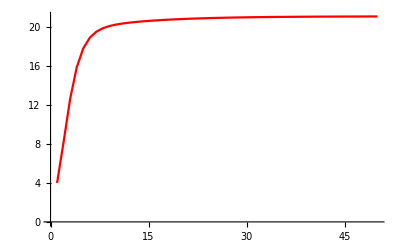

```mathematica
avgPlot3=ListLinePlot[Table[Nmtrx2[[;;,t]].Reverse[Table[i,{i,0,nMax}]],{t,1,nSteps}],PlotStyle->Red,PlotRange->All]
```

## Allele Frequency

### Density Independent

```mathematica
pmtrx=Import["/Users/ailenemacpherson/Dropbox/r:K selection files/MatLab/DIp.csv"]//Chop;
```

```mathematica
{nBins,tMax}=Dimensions[pmtrx]-{0,1}
```

{10,50}

```mathematica
pmtrx2=Transpose[Table[Reverse[pmtrx[[;;,c]]],{c,1,tMax+1}]];
```

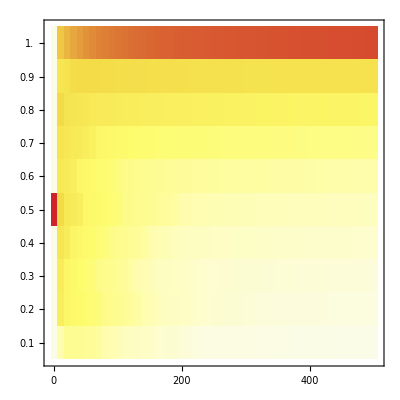

```mathematica
mtrxPlot4=MatrixPlot[pmtrx2,AspectRatio->1,ColorFunction->"TemperatureMap",FrameTicks->{Table[{i,1-(i-1)/nBins//N},{i,1,nBins}],Table[{t,(t-1)*Δt},{t,1,tMax+1,10}],False,False}]
```

```mathematica
Avg=Import["/Users/ailenemacpherson/Dropbox/r:K selection files/MatLab/DIAvg.csv"]//Chop;
```

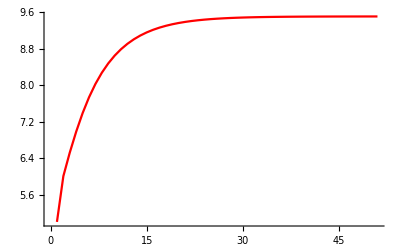

```mathematica
avgPlot4=ListLinePlot[Avg[[;;,2]]*nBins,PlotRange->All,PlotStyle->Red]
```

### Density Dependent

```mathematica
pmtrx=Import["/Users/ailenemacpherson/Dropbox/r:K selection files/MatLab/DDp.csv"]//Chop;
```

```mathematica
{nBins,tMax}=Dimensions[pmtrx]-{0,1}
```

{10,50}

```mathematica
pmtrx2=Transpose[Table[Reverse[pmtrx[[;;,c]]],{c,1,tMax+1}]];
```

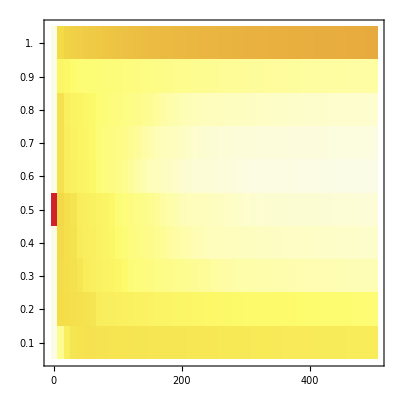

```mathematica
mtrxPlot5=MatrixPlot[pmtrx2,AspectRatio->1,ColorFunction->"TemperatureMap",FrameTicks->{Table[{i,1-(i-1)/nBins//N},{i,1,nBins}],Table[{t,(t-1)*Δt},{t,1,tMax+1,10}],False,False}]
```

```mathematica
Avg=Import["/Users/ailenemacpherson/Dropbox/r:K selection files/MatLab/DDAvg.csv"]//Chop;
```

```mathematica
Avg
```

{{4,0.5},{8.2275,0.44024},{12.653,0.40748},{15.88,0.39293},{17.836,0.38709},{18.939,0.38515},{19.557,0.38493},{19.917,0.38547},{20.14,0.38633},{20.291,0.38732},{20.401,0.38833},{20.487,0.38933},{20.558,0.39029},{20.618,0.39121},{20.671,0.39207},{20.717,0.3929},{20.758,0.39367},{20.795,0.39441},{20.829,0.39511},{20.859,0.39577},{20.886,0.3964},{20.911,0.39699},{20.933,0.39756},{20.953,0.39811},{20.971,0.39863},{20.987,0.39912},{21.002,0.3996},{21.016,0.40006},{21.028,0.4005},{21.039,0.40093},{21.049,0.40134},{21.058,0.40174},{21.066,0.40212},{21.073,0.4025},{21.08,0.40286},{21.086,0.40321},{21.091,0.40355},{21.096,0.40389},{21.1,0.40421},{21.104,0.40453},{21.108,0.40484},{21.111,0.40515},{21.114,0.40545},{21.116,0.40574},{21.119,0.40602},{21.121,0.4063},{21.123,0.40658},{21.124,0.40685},{21.126,0.40712},{21.127,0.40738},{21.128,0.40764}}

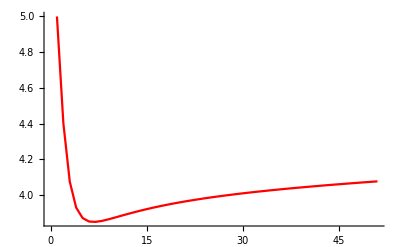

```mathematica
avgPlot5=ListLinePlot[Avg[[;;,2]]*nBins,PlotRange->All,PlotStyle->Red]
```

Combined Plots

## Population sizes

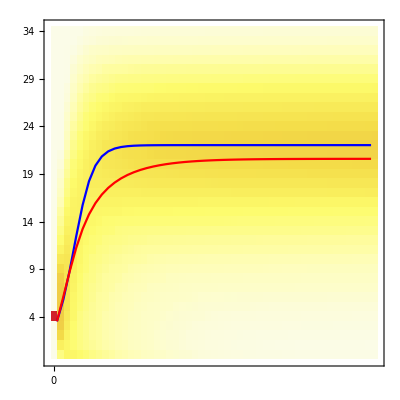

```mathematica
DIN=Show[{mtrxPlot2,detPlot2,avgPlot2}]
```

```mathematica
Export["/Users/ailenemacpherson/Documents/OutPut/DIN.gif",DIN,ImageResolution->700]
```

/Users/ailenemacpherson/Documents/OutPut/DIN.gif

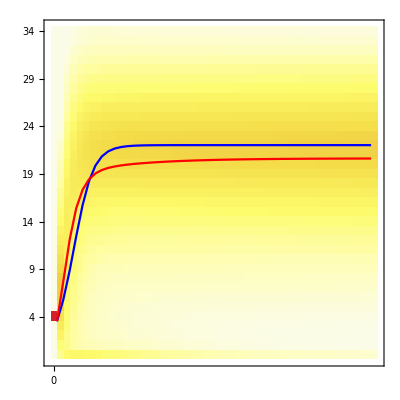

```mathematica
DDN=Show[{mtrxPlot3,detPlot2,avgPlot3}]
```

```mathematica
Export["/Users/ailenemacpherson/Documents/OutPut/DDN.gif",DDN,ImageResolution->700]
```

/Users/ailenemacpherson/Documents/OutPut/DDN.gif

## Allele Frequencies

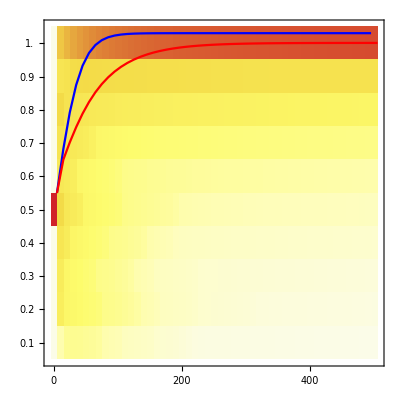

```mathematica
DIp=Show[{mtrxPlot4,detPlot4,avgPlot4}]
```

```mathematica
Export["/Users/ailenemacpherson/Documents/OutPut/DIp.gif",DIp,ImageResolution->700]
```

/Users/ailenemacpherson/Documents/OutPut/DIp.gif

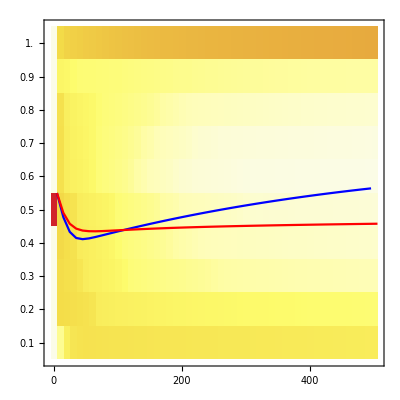

```mathematica
DDp=Show[{mtrxPlot5,detPlot5,avgPlot5}]
```

```mathematica
Export["/Users/ailenemacpherson/Documents/OutPut/DDp.gif",DDp,ImageResolution->700]
```

/Users/ailenemacpherson/Documents/OutPut/DDp.gif